# Logic-“Digital System” Related

Dali Lai

A combinational logic circuit is one whose output depend only on its current combination of input values, and a Logical Expression is an Expression that uses one or more conditions to return a true or false value.
 It’s useful to have a single line of code instead of tens, hundreds of states hard coded line by line. This essay will be a brief introduction starting from logic gates, by showing the simulation of the circuit with Wolfram software System Modeler, multiple gates combinational circuit, K-map, Demogan’s Law, and theirs application.

1. Combinational Circuit-logic gate

By combining different logic gates (AND, NAND, OR...etc.) a circuit is created. Such circuit transforms its  inputs into the desired output. In circuit-logic programming, inputs-outputs table is known as a truth table.

Here is an example of a logic gate, the OR-gate, X || Y:

```mathematica
WebImageSearch[#,"Images",Method->"Google"]&["or gate"][[4]]
```

Formatted as a multiple entry array, inputs-output table is known as Karnaugh map (k-map). For the OR-gate example above it is:

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x||y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | True | True
0 | True | False

Let’s simulate the logic gate OR with 2 inputs in SystemModeler, a software that models circuits behaviors amongst other things.

Our system is an Or-gate with two ports each receiving a stepwise electrical signal.

```mathematica
orGateConnectedToDigitalgEntries=-Graphics-;
```

```mathematica
orgate=SystemModelPlot[SystemModelSimulate[orGateConnectedToDigitalgEntries,{0,0.5}],{"pulse1.y","pulse2.y"},];
```

Each input is cyclic, described in terms of its ‘% duty’ which is the ratio of time spent at max voltage to time spent at low voltage. The simulated output is constant and maximal in voltage (4 volts ⇔ True) when one of the entries is also. As predicted by the table.

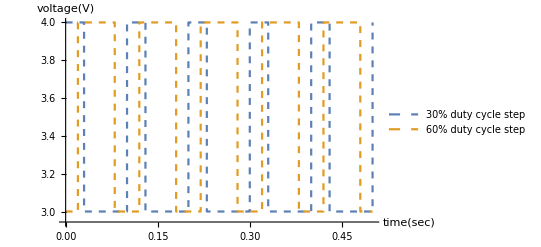
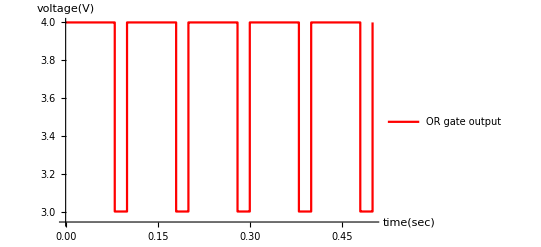

```mathematica
Column[{orgate,SystemModelPlot[SystemModelSimulate[orGateConnectedToDigitalgEntries,{0,0.5}],{"orGate1.y"},]}]
```

Another example for XOR gate:

Let’s simulate the logic gate XOR with 2 inputs in SystemModeler, a software that models circuits behaviors amongst other things.

```mathematica
WebImageSearch[#,"Images",Method->"Google"]&["xor gate"][[5]]
```

-Graphics-

Here is the K-map of the XOR gate, rearranged from the truth table.

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x⊻y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | False | True
0 | True | False

Our system is an Or-gate with two ports each receiving a stepwise electrical signal.

```mathematica
xorGateConnectedToDigitalgEntries=-Graphics-;
xorgate=SystemModelPlot[SystemModelSimulate[xorGateConnectedToDigitalgEntries,{0,0.5}],{"pulse1.y","pulse2.y"},];
```

The simulated output is constant and maximal in voltage (4 volts ⇔ True) when the entries are in different states. As predicted by the table.

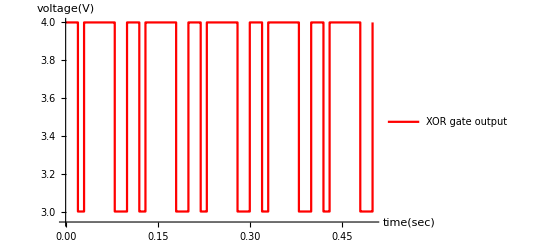
-Graphics-
-Graphics-

```mathematica
Column[{xorgate,SystemModelPlot[SystemModelSimulate[xorGateConnectedToDigitalgEntries,{0,0.5}],{"xorGate1.y"},]}]
```

2. Combinational Circuit-multiple inputs/gates

This is about the combination of logic gates, and its application.  So here are some examples of combining circuit examples with more than 2 inputs. It is harder to calculate the input-output truth table.
Lets take a 4 inputs combinational circuit:

Here is the truth table of the new nand logic gate that we introduce (nor gate simply produce the opposite output that the previously seen or-gate)

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x⊼y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | False | True
0 | True | True

Our new model now combines all four gates:

```mathematica
fourGateConnectedToDigitalgEntries=-Graphics-;
```

Below  is the timing diagram simulated the above circuit:

```mathematica
fourinput=SystemModelPlot[SystemModelSimulate[fourGateConnectedToDigitalgEntries,{0,0.5}],{"pulse1.y","pulse2.y","pulse3.y","pulse4.y"},];
```

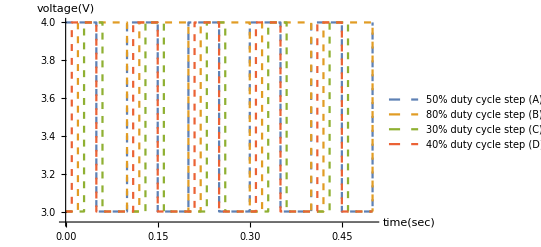
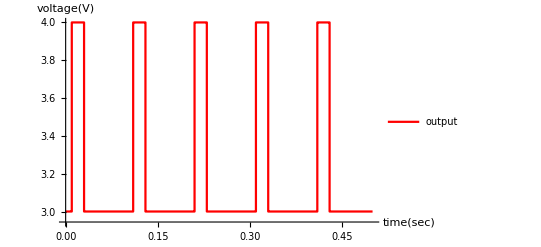

```mathematica
Column[{fourinput,SystemModelPlot[SystemModelSimulate[fourGateConnectedToDigitalgEntries,{0,0.5}],{"xorGate1.y"},]}]
```

By writing the whole expression by hand from the circuit, one can get the output logic expression is equal to:

```mathematica
((A∨B∨C)⊼(C))⊻(C⊽D)
```

However ... it’ s still not very clear what the output is just by looking the logic expression. So some simplification is required.

The whole logic expression, most of the time (not take into account timing hazard), can be simplified using different axioms of switching algebra , Demorgan’s law...etc. Here is the K-map for the above original logic expression:

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[((A∨B∨CC)⊼(CC))⊻(CC⊽DD),{A,B},{CC,DD}],{"11","10","01","00"}],{"CD/AB","11","10","01","00"}}],Frame->All]
```

CD/AB | 11 | 10 | 01 | 00
11 | False | False | True | False
10 | False | False | True | False
01 | False | False | True | False
00 | False | False | True | False

Here is the simplification form of the above logic expression.

```mathematica
BooleanMinimize[((A∨B∨C)⊼(C))⊻(C⊽D)]
```

!C&&D

Showing the truth table for the simplified form of the logic expression.

```mathematica
BooleanTable[!c&&d,{c,d}]
```

{False,False,True,False}

This confirms that the output of this logic circuit won’t depends on A and B. This is observed in the simulation and in practice (most likely).

Takeaway: Timing diagram, K-map, logic expression are ways to represent the behavior of the combinational circuit, depends on how one wants to represent, one can be more useful than others, but they are all interchangeable.

## 3. Demorgan’s Law

“A logically equivalent circuit can be formed by taking the dual of the operator(s) and complementing all the inputs and outputs.”
Demorgan’s law is useful when minimizing logic expression as well as in practice. Let’s say to perform a ⊼ (nand) expression, and the only IC chip left in the lab are AND, OR, NOT (know as inverter), of course one can build an NAND gate by combining a AND gate with a NOT gate. In practice however, it is preferable, to use  as few IC chips as possible to obtain faster computations (propagation delay) and lower costs.    

As an example we will show:

#### ¬(A ∧ B) ≡ (¬A) ∨ (¬B)

K-map for A NAND B:

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[A⊼B,{A},{B}],{"1","0"}],{"A/B","1","0"}}],Frame->All]
```

A/B | 1 | 0
1 | False | True
0 | True | True

K-map for (NOT A) OR (NOT B):

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[!A∨!B,{A},{B}],{"1","0"}],{"A/B","1","0"}}],Frame->All]
```

A/B | 1 | 0
1 | False | True
0 | True | True

Also, another way to show.

```mathematica
SatisfiableQ[!(a&&b)&&(!a||!b),{a,b}]
```

```mathematica
True
```

## 4. Applications

Knowing that giving a logic expression, one can get a truth table (and k-map), but this can go other way around. 
Let’s say one wants to only let the output be on when a specific input set is engaged, for example like a digital password, displaying numbers or words...etc.
Knowing the logic expression makes programming on FPGA board much simpler since simply implementing a logic expression is much easy to understand and debug than hard coding 2^8 states.

```mathematica
Manipulate[Row[{Grid[MapThread[Prepend,{Prepend[BooleanTable[BooleanFunction[FromDigits[{q,w,e,r,t,y,u,i},2],{a,b,c}],{a},{b,c}],{"11","10","01","00"}],{"bc/a","1","0"}}],Frame->All],
BooleanFunction[FromDigits[{q,w,e,r,t,y,u,i},2],{a,b,c}]}],]
```

## 5. Future function/ Conclusion

What if there are more than 4 variables? What would the map be like? 
Import["C:\Users\dali7\Pictures\lec-5-combinational-logic-kmaps2-9-638.jpg"]
-Graphics-
Therefore, a 3D K-map will be used,  a 3D K-map which the operator can rotate the K-map planes around and visualize will be helpful for understanding especially for students who first time finding the Min/Max terms more than 4 variables K-map by hand. 
For the application aspect, most of the time, FPGA board programmers only knows when the output should be on when a specific set of input is received, so finding the logic expression is the main point.

Combining the ability of simulating circuit as well as truth table , one can do some basic digital design with these tools and functions.